## Tutorial: Haldane model

This is a notebook for the first steps for the use of the HyperBloch package for efficient modeling of tight-binding models on hyperbolic lattices.

## Preliminaries:

### Remark:

Before using the getting started with the HyperBloch notebook:

Make sure that the HyperBloch package is installed, if this is not the case please follow the instruction on the website (link to website ???).

Make sure that the required files .hcc,  .hcm and .hcs files are in the current directory. This entails files:

(2,4,6)_T2.2_3.hcc

{6,4}-tess-NNN_T2.2_3.hcm

{6,4}-tess-NNN_T2.2_3_sc-T5.4.hcs

{6,4}-tess-NNN_T2.2_3_sc-T9.3.hcs

In case no such files exists, please follow the instructions in the the prerequisites section on the website (link to website ???) or download it there.

### Load the HyperBloch package:

```mathematica
<<PatrickMLenggenhager`HyperBloch`
```

HyperBloch - Version 0.9.1
Main author: Patrick M. Lenggenhager

This package loads the following dependencies:
	- L2Primitives by Srdjan Vukmirovic
	- NCAlgebra by J. William Helton and Mauricio de Oliveira

```mathematica
SetDirectory[NotebookDirectory[]];
```

Open the documentation:

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage"];
```

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/guide/HyperBlochPackage"];
```

### Needed functions:

```mathematica
ComputeEigenvalues[cfH_,pgMat_,Npts_,Nruns_,genus_]:=
Flatten@ParallelTable[
Flatten@Table[
Eigenvalues[cfH@@(pgMat.RandomReal[{-Pi,Pi},2genus])],{i,1,Round[Npts/Nruns]}],
{j,1,Nruns},Method->"FinestGrained"]
```

### Import cells

We first import the cell, model, and supercell model graphs as produced by the HyperCells package:

We consider the following sequence of supercells, defined in terms of quotients given in https://www.math.auckland.ac.nz/~conder/TriangleGroupQuotients101.txt by M. Conder, (the cell “T2.6” is the primitive cell):

```mathematica
cells={"T2.2","T5.4","T9.3"};
```

Cell graph:

```mathematica
pcell=ImportCellGraphString[Import["(2,4,6)_T2.2_3.hcc"]];
```

Primitive cell:

```mathematica
pcmodel=ImportModelGraphString[Import["{6,4}-tess-NNN_T2.2_3.hcm"]];
```

Supercells:

```mathematica
scmodels=Association[#->
ImportSupercellModelGraphString[ 
Import[ToString@StringForm["{6,4}-tess-NNN_T2.2_3_sc-``.hcs",#]]]
&/@cells[[2;;]]];
```

Extract genus:

```mathematica
genusLst=Join[
Association[cells[[1]]->pcmodel["Genus"]],
Association[#->(scmodels[#])["Genus"]&/@cells[[2;;]]]
];
```

### Import point-group matrices:

```mathematica
pgMatSc=Association[#->
ImportPGMatrixString[ 
Import[ToString@StringForm["(2,4,6)_``_3_PGMatrix_c.g",#]],sparse->True]
&/@cells];
```

## {6,4} Haldane model:

### Constructing Hamiltonians:

#### Hopping amplitudes:

#### Mass term, resp. staggered potential:

```mathematica
mVec =M0{1,-1,1,-1,1,-1};
onsitePC=AssociationThread[VertexList@pcmodel["Graph"]->mVec];
```

#### NN- and NNN-hopping terms:

```mathematica
fm=Exp[-ⅈ ϕ];fp= Exp[ⅈ ϕ] ;
```

```mathematica
nnVec=ConstantArray[h1,12];
nnnVec=ConstantArray[h2 fp,24];
hoppingVec=Join[nnVec,nnnVec];
```

```mathematica
hoppingsPC=AssociationThread[EdgeList@pcmodel["Graph"]->hoppingVec];
```

#### Hamiltonians:

Primitive cell:

The Hamiltonian for the nearest-neighbor tight-binding model on the primitive cell T2.2 is:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,1,onsitePC,hoppingsPC,CompileFunction->True];
```

Supercells:

The Hamiltonians for the nearest - neighbor tight - binding model on the sequence of supercells are, (this might take a minute):

```mathematica
Hclst=
Join[Association["T2.2"->Hpc],
Association[#->
AbelianBlochHamiltonian[scmodels[#],1,onsitePC,hoppingsPC,PCModel->pcmodel,CompileFunction->True]
&/@cells[[2;;]]]];
```

### Density of states:

Let us compute the density of states by exact diagonalization.

Compute the Eigenvalues via 10^4 momentum random samples, (this might take a minute):

```mathematica
evals=Association[#->ComputeEigenvalues[Hclst[#]/.{h1->1,h2->0.5, M0->0,ϕ->π/2},pgMatSc[#]["MatrixList"]["c"],10^4,32,genusLst[#]]&/@cells];
```

Visualize density of states via a kernel density estimation, (this might take a minute):

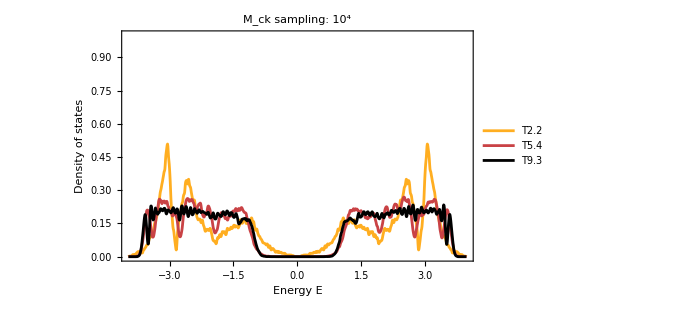

```mathematica
SmoothHistogram[evals,0.01,"PDF",Frame->True,FrameStyle->Black,FrameLabel->{"Energy E","Density of states"},PlotRange->{0,1}, LabelStyle->20,PlotLabel->"M_ck sampling: 10^4",PlotStyle->(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,3]/3.)),ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},Background->None]
```

```mathematica
NotebookSave[]
```